### Categorization

Tech Note

StianRamsnes/MaXrd

StianRamsnes`MaXrd`

StianRamsnes/MaXrd/tutorial/UsingTheRotationOptions

### Keywords

# Using the rotation options

Some of the tools that deal with creation and manipulation of crystal entities – asymmetric units, unit cells, blocks, domains and structures – allow rotation of these instances. These functions share a common options framework which will be elaborated on here.

"RotationAnchorReference" | describe the type of rotation anchors that will be used
"RotationAnchorShift" | an optional translation of the anchor point(s)
"RotationAxes" | define the three rotation axes to be used in 3D rotations
"RotationMap" | maps domains to their respective rotation amounts

An overview of the rotation options encountered in the relevant functions.

The functions that currently make use of the rotation options are:

DomainPlot | provides a visual plot of a domain representation
EmbedStructure | embeds given units into a host system
SynthesiseStructure | assembles a given domain to the represented structure

The relevant functions along with short descriptions.

Load the package if not done already:

```mathematica
<<MaXrd`
```

## Anchors

By anchor we mean the particular point a rotation will be performed about. The first option, "RotationAnchorReference" enables us to choose between four general positions of the anchor(s):

"Host" | origin of the host structure
"Domain" | origin of each domain's cell that is closest to the host's origin
"DomainCentroid" | centroid of each domain
"Unit" | origin of each unit

All the possible settings of the "RotationAnchorReference" option and what they mean.

We will start an example using DomainPlot:

This will be the domain we'll be working with in this demo:

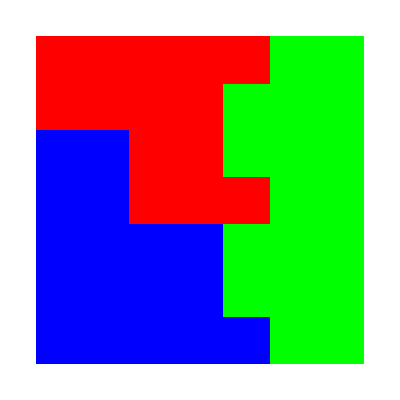

```mathematica
domain={{7,7,1},{3,3,3,3,3,1,1,3,3,3,3,3,1,1,3,3,3,1,1,1,1,3,3,3,1,1,1,1,3,2,2,1,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2}};
DomainPlot@domain
```

Before we start rotating let us define a map for all the anchors that can come up with this particular domain:

```mathematica
anchors=<|
"Host"->{{0.,0.}},
"Domain"->{{0.,0.},{2.,3.},{4.,1.}},
"DomainCentroid"->{{1.912,2.029},{2.643,5.286},{5.667,3.500}},
"Unit"->{{0.,5.},{0.,6.},{1.,5.},{1.,6.},{2.,3.},{2.,4.},{2.,5.},{2.,6.},{3.,3.},{3.,4.},{3.,5.},{3.,6.},{4.,3.},{4.,6.}}|>;
```

The anchor points defined above are produced internally by the functions, but not directly obtainable. They are therefore copied here. We will momentarily be using them to show graphically where they are.

Below is an interactive controller to illustrate the various anchor reference settings. The yellow dots indicate where the anchors are (to avoid cluttering, only the red cells have the anchors shown in the "Unit" setting).

```mathematica
Manipulate[
Graphics[{
First@DomainPlot[domain,
"RotationMap"-><|1->θ1*Degree,2->θ2*Degree,3->θ3*Degree|>,
"RotationAnchorReference"->r],
{Yellow,Disk[#,0.25]&/@anchors@r}
}],
{{θ1,0,"Red"},0,90},{{θ2,0,"Green"},0,90},{{θ3,0,"Blue"},0,90},
{{r,"DomainCentroid","Type"},{"Host","Domain","DomainCentroid","Unit"}},
ControlPlacement->Right]
```

If you need further control of where the anchors should be, use the option "RotationAnchorShift" to translate the anchor(s).

### A practical example

Now that we're more familiar with the anchors, let us look at a more practical example. We will create two layers where the top sheet should be rotated. Then, we will synthesise the structure with graphene. First, let us make a general factory method that creates the layered domain:

Our demo structure will consist of 7×7×2 unit cells:

```mathematica
makeSandwichedDomains[A_,B_,C_]:={{A,B,C},Flatten@ConstantArray[Range@C,A*B]}
domain=makeSandwichedDomains[7,7,2];
DomainPlot@domain
```

-Graphics3D-

We wish to rotate the top layer, for instance by 15° and hinged at the lower-left corner:

```mathematica
DomainPlot[domain,
"RotationMap"-><|2->{0,0,15°}|>,
"RotationAnchorReference"->"Host"]
```

-Graphics3D-

The next step is to assemble this structure. Here we want to use graphene in both layers, but we need to create it first for our $CrystalData and expand it to one unit cell (which each block represents):

ImportCrystalData is normally used with cif files, but here it's just as simple to provide the details “manually”:

```mathematica
ImportCrystalData[
{"Graphene","C","P-3m1"},
{2.5,2.5,5.0,90,90,120},
{<|"Element"->"C","FractionalCoordinates"->{1/3,2/3,1/2}|>}];
ExpandCrystal["Graphene","NewLabel"->"GrapheneCell"]
```

GrapheneCell

Finally, we synthesise the «domain structure». We make use of the third parameter to replace all the domain identifiers (1's and 2's) with the label of the graphene unit cell. We use the same rotation options as above, and we see that the "RotationMap" still differentiates between the two domains.

The realisation of our domain model to a crystal structure is done with SynthesiseStructure:

```mathematica
SynthesiseStructure[domain,"GrapheneLayers",<|_Integer->"GrapheneCell"|>,
"RotationMap"-><|2->{0,0,15°}|>,
"RotationAnchorReference"->"Host"
];
CrystalPlot["GrapheneLayers"]
```

-Graphics3D-

## The common auxiliary function

The functions that currently use the rotation options framework all rely internally on the "RotationTransformation" module of InputCheck. This procedure returns a TransformationFunction that in turn requires one or two parameters, depending on the dimensions and anchor reference type of input.

In this first example we create a two-dimensional domain to be used in the InputCheck function. It uses "Domain" anchor reference, so only the domain identifier is required at later input.

Constructing a two-dimensional domain:

```mathematica
domain1=ConstructDomains[{7,7,1},3,8]
```

{{7,7,1},{3,3,3,3,2,2,2,3,3,3,3,2,2,2,3,2,3,3,2,2,2,2,2,3,3,3,2,2,3,2,3,2,2,2,2,2,1,1,2,2,2,2,2,1,1,2,1,2,2}}

Obtaining the transformation function where we want to rotate all cells of domain 3 around the “domain corner” by 23.5°:

```mathematica
R1=InputCheck["RotationTransformation",domain1,{{0,0,0},"Domain",<|3->23.5°|>}]
```

MaXrd`Private`R$17918

To get the appropriate transformation function, we only need to specify the domain identifier:

```mathematica
R1[3]
```

TransformationFunction[(0.91706 | -0.398749 | 0.
0.398749 | 0.91706 | 0.
0. | 0. | 1.)]

In this second example we use a three-dimensional structure instead and choose to rotate about each block as well. Thus, we specify both the domain and the point in order to get the transformation function back:

```mathematica
domain2=ConstructDomains[{7,7,7},3,250];
R2=InputCheck["RotationTransformation",domain2,{{0,0,0},"Unit",<|1->{0,0,45°}|>}];
R2[1,{2.5,3.5,0.5}]
```

TransformationFunction[(0.707107 | -0.707107 | 0. | 3.20711
0.707107 | 0.707107 | 0. | -0.742641
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.)]

Related Guides

Related Tech Notes